```mathematica
data=Import["/Users/miguel/Documents/Internship_CENTURI/data/gc_wt.csv", "Dataset", "HeaderLines"->1]
```

```mathematica
linLogFit = Fit[data[All,"A5"]//Normal, {1, x, 1/(1+Exp[-x])}, x]
```

-0.878103+1.0978/(1+ⅇ^-x)+0.00127462 x

```mathematica
linLogPython[x_]:= 3.65575890*^-1/Power[1 + 8.27781271*^-1 * Exp[-2.54145114*^-1 * x],4.54612599*^8]+8.44131740*^-4*x +1.76633941*^-2
```

```mathematica
linLogPython[0]
```

General::munfl: 0.365576 2.00968×10^-119074052 is too small to represent as a normalized machine number; precision may be lost.

0.0176634

General::munfl: 0.365576 8.584224×10^-97712715 is too small to represent as a normalized machine number; precision may be lost.

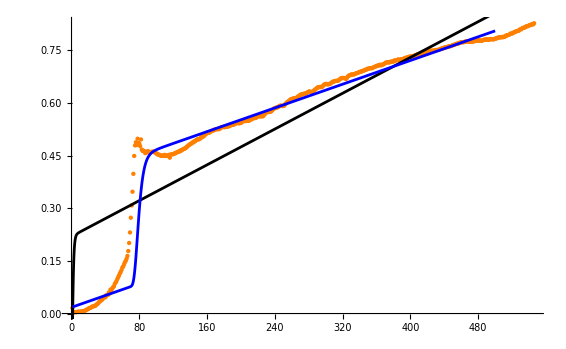

```mathematica
Show[ListPlot[Normal[data[All,"A5"]], PlotStyle->Orange], Plot[linLogFit, {x,0,500}, PlotStyle->{Black}] , Plot[linLogPython[x], {x,1,500}, PlotStyle->{Blue}] ]
```

```mathematica
K
```

K

General::munfl: 0.365576 8.584224×10^-97712715 is too small to represent as a normalized machine number; precision may be lost.

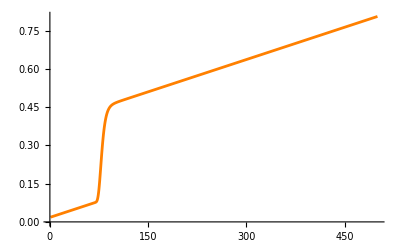

```mathematica
Plot[linLogPython[x], {x,1,500}, PlotStyle->Orange]
```

Let’s try the nonlinear fit function. According to the documentation this function assumes that the data is normally distributed. How much of an assumption is this in our case?

```mathematica
nlm=NonlinearModelFit[data[All,"A5"]//Normal,{k/Power[1 +Q*Exp[-B * x], 1/ν] + m*x + bb, Q>0, k>0, m>0, ν >0, bb>0},{k, Q, B, ν, m,bb},x]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

Part::partw: Part 4 of -Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$39144={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{1,6,817},«1»}},{«1»},{908,«6»,None},{None,None,None}][…[«1»]] does not exist.

Part::partw: Part 5 of -Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$39144={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{1,6,817},«1»}},{«1»},{908,«6»,None},{None,None,None}][…[«1»]] does not exist.

Part::partw: Part 6 of -Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$39144={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{1,6,817},«1»}},{«1»},{908,«6»,None},{None,None,None}][…[«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Overflow[] is not a real number at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[]} is not a list of real numbers with dimensions {6} at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

Set::partw: Part 4 of 0.995 «1»«1»Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$39144={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{«1»},«1»}},«1»,{908,«6»,None},{None,None,None}][«1»] does not exist.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit::nrnum: The function value Overflow[] is not a real number at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrlnum: The function value {Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[]} is not a list of real numbers with dimensions {6} at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrlnum will be suppressed during this calculation.

Set::partw: Part 4 of 0.995 «1»«1»Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$39357={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{«1»},«1»}},«1»,{908,«6»,None},{None,None,None}][«1»] does not exist.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit[{0.016,0.004,0.004,0.004,0.004,0.004,0.005,0.005,0.005,0.005,0.005,0.006,0.006,0.007,0.007,0.008,0.01,0.011,0.012,0.014,0.015,0.016,0.017,0.019,0.02,0.021,0.021,0.022,0.025,0.026,0.028,0.031,0.034,0.035,0.04,0.039,0.042,0.046,0.048,0.046,0.052,0.052,0.053,0.06,0.057,0.068,0.066,0.071,0.075,0.077,0.084,0.088,0.092,0.098,0.103,0.108,0.114,0.118,0.124,0.131,0.134,0.14,0.146,0.15,0.156,0.164,0.178,0.201,0.231,0.273,0.308,0.347,0.398,0.449,0.479,0.488,0.48,0.498,0.486,0.484,0.477,0.496,0.467,0.463,0.464,0.462,0.457,0.46,0.459,0.463,0.461,0.459,0.46,0.46,0.461,0.461,0.461,0.459,0.459,0.457,0.454,0.454,0.452,0.452,0.45,0.449,0.45,0.45,0.449,0.452,0.449,0.45,0.45,0.45,0.452,0.444,0.453,0.453,0.454,0.454,0.455,0.457,0.457,0.459,0.46,0.461,0.461,0.464,0.463,0.466,0.467,0.468,0.47,0.47,0.472,0.475,0.476,0.479,0.481,0.482,0.484,0.485,0.488,0.488,0.491,0.491,0.494,0.495,0.497,0.496,0.497,0.499,0.503,0.502,0.505,0.505,0.508,0.51,0.512,0.515,0.516,0.515,0.516,0.518,0.52,0.52,0.522,0.522,0.524,0.525,0.525,0.525,0.526,0.525,0.527,0.528,0.531,0.531,0.532,0.531,0.531,0.532,0.532,0.533,0.533,0.534,0.536,0.536,0.537,0.538,0.538,0.539,0.54,0.542,0.543,0.544,0.542,0.542,0.543,0.543,0.545,0.547,0.549,0.55,0.548,0.55,0.55,0.549,0.549,0.55,0.552,0.553,0.554,0.556,0.557,0.557,0.557,0.558,0.561,0.562,0.562,0.562,0.562,0.562,0.562,0.562,0.565,0.568,0.57,0.574,0.574,0.574,0.574,0.575,0.575,0.577,0.579,0.582,0.584,0.585,0.586,0.587,0.587,0.589,0.59,0.592,0.592,0.592,0.591,0.592,0.592,0.596,0.598,0.601,0.603,0.604,0.607,0.608,0.611,0.611,0.612,0.613,0.613,0.613,0.613,0.615,0.618,0.619,0.621,0.623,0.624,0.624,0.625,0.626,0.626,0.627,0.628,0.629,0.631,0.632,0.633,0.631,0.631,0.631,0.633,0.635,0.637,0.639,0.641,0.643,0.645,0.645,0.645,0.646,0.645,0.646,0.649,0.652,0.653,0.654,0.654,0.653,0.653,0.654,0.654,0.656,0.658,0.66,0.66,0.662,0.662,0.663,0.663,0.663,0.664,0.666,0.668,0.67,0.671,0.671,0.671,0.671,0.67,0.668,0.671,0.675,0.677,0.679,0.679,0.681,0.681,0.681,0.681,0.682,0.683,0.685,0.685,0.686,0.687,0.688,0.689,0.689,0.691,0.691,0.692,0.694,0.694,0.695,0.697,0.697,0.698,0.699,0.699,0.699,0.699,0.701,0.702,0.703,0.704,0.705,0.706,0.707,0.707,0.709,0.707,0.708,0.709,0.71,0.711,0.713,0.715,0.715,0.716,0.716,0.715,0.717,0.717,0.718,0.718,0.718,0.721,0.72,0.722,0.722,0.723,0.724,0.722,0.723,0.724,0.725,0.724,0.726,0.727,0.728,0.729,0.729,0.73,0.731,0.732,0.732,0.732,0.733,0.733,0.734,0.735,0.736,0.737,0.738,0.738,0.739,0.74,0.74,0.74,0.741,0.741,0.742,0.743,0.743,0.744,0.745,0.746,0.747,0.748,0.749,0.749,0.748,0.749,0.749,0.75,0.751,0.75,0.751,0.751,0.752,0.753,0.754,0.755,0.756,0.756,0.758,0.758,0.759,0.759,0.76,0.761,0.761,0.762,0.762,0.763,0.765,0.765,0.766,0.767,0.768,0.769,0.769,0.77,0.771,0.772,0.773,0.773,0.773,0.773,0.774,0.775,0.775,0.775,0.775,0.775,0.774,0.774,0.775,0.775,0.775,0.776,0.776,0.777,0.777,0.777,0.778,0.778,0.778,0.777,0.777,0.778,0.779,0.78,0.781,0.78,0.781,0.781,0.78,0.78,0.782,0.782,0.782,0.781,0.781,0.782,0.783,0.784,0.784,0.786,0.786,0.787,0.787,0.787,0.788,0.787,0.788,0.788,0.791,0.791,0.793,0.793,0.794,0.795,0.797,0.798,0.798,0.799,0.801,0.802,0.803,0.804,0.805,0.805,0.806,0.809,0.81,0.81,0.813,0.814,0.814,0.815,0.817,0.818,0.819,0.819,0.821,0.822,0.822,0.824,0.824,0.824,0.827},{bb+k (1+ⅇ^(-B x) Q)^(-1/ν)+m x,Q>0,k>0,m>0,ν>0,bb>0},{k,Q,B,ν,m,bb},x]

```mathematica
nlm["BestFitParameters"]
```

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General::ovfl will be suppressed during this calculation.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

Part::partw: Part 4 of -Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$40847={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{1,6,817},«1»}},{«1»},{908,«6»,None},{None,None,None}][…[«1»]] does not exist.

Part::partw: Part 5 of -Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$40847={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{1,6,817},«1»}},{«1»},{908,«6»,None},{None,None,None}][…[«1»]] does not exist.

Part::partw: Part 6 of -Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$40847={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{1,6,817},«1»}},{«1»},{908,«6»,None},{None,None,None}][…[«1»]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

NonlinearModelFit::nrnum: The function value Overflow[] is not a real number at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

NonlinearModelFit::nrgnum: The gradient is not a vector of real numbers at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

General::stop: Further output of NonlinearModelFit::nrgnum will be suppressed during this calculation.

NonlinearModelFit::nrlnum: The function value {Overflow[],Overflow[],Overflow[],Overflow[],Overflow[],Overflow[]} is not a list of real numbers with dimensions {6} at {k,Q,B,ν,m,bb} = {1.,2.34998,-4.37262×10^29,1.,1.,1.}.

Set::partw: Part 4 of 0.995 «1»«1»Experimental`NumericalFunction[{Hold[Block[{x={«546»},Optimization`FindFit`y$40847={«546»}},1/2 Subtract[«2»].Subtract[«2»]]],Block},{0,{{{},1,0,Hold[k],0,0},{{},1,1,Hold[Q],0,0},{{},1,2,Hold[B],0,0},{{},1,3,Hold[ν],0,0},{{},1,4,Hold[m],0,0},{{},1,5,Hold[bb],0,0}}},{{{«1»},«1»}},«1»,{908,«6»,None},{None,None,None}][«1»] does not exist.

NonlinearModelFit::conv: Interior point method fails to converge.

NonlinearModelFit[{0.016,0.004,0.004,0.004,0.004,0.004,0.005,0.005,0.005,0.005,0.005,0.006,0.006,0.007,0.007,0.008,0.01,0.011,0.012,0.014,0.015,0.016,0.017,0.019,0.02,0.021,0.021,0.022,0.025,0.026,0.028,0.031,0.034,0.035,0.04,0.039,0.042,0.046,0.048,0.046,0.052,0.052,0.053,0.06,0.057,0.068,0.066,0.071,0.075,0.077,0.084,0.088,0.092,0.098,0.103,0.108,0.114,0.118,0.124,0.131,0.134,0.14,0.146,0.15,0.156,0.164,0.178,0.201,0.231,0.273,0.308,0.347,0.398,0.449,0.479,0.488,0.48,0.498,0.486,0.484,0.477,0.496,0.467,0.463,0.464,0.462,0.457,0.46,0.459,0.463,0.461,0.459,0.46,0.46,0.461,0.461,0.461,0.459,0.459,0.457,0.454,0.454,0.452,0.452,0.45,0.449,0.45,0.45,0.449,0.452,0.449,0.45,0.45,0.45,0.452,0.444,0.453,0.453,0.454,0.454,0.455,0.457,0.457,0.459,0.46,0.461,0.461,0.464,0.463,0.466,0.467,0.468,0.47,0.47,0.472,0.475,0.476,0.479,0.481,0.482,0.484,0.485,0.488,0.488,0.491,0.491,0.494,0.495,0.497,0.496,0.497,0.499,0.503,0.502,0.505,0.505,0.508,0.51,0.512,0.515,0.516,0.515,0.516,0.518,0.52,0.52,0.522,0.522,0.524,0.525,0.525,0.525,0.526,0.525,0.527,0.528,0.531,0.531,0.532,0.531,0.531,0.532,0.532,0.533,0.533,0.534,0.536,0.536,0.537,0.538,0.538,0.539,0.54,0.542,0.543,0.544,0.542,0.542,0.543,0.543,0.545,0.547,0.549,0.55,0.548,0.55,0.55,0.549,0.549,0.55,0.552,0.553,0.554,0.556,0.557,0.557,0.557,0.558,0.561,0.562,0.562,0.562,0.562,0.562,0.562,0.562,0.565,0.568,0.57,0.574,0.574,0.574,0.574,0.575,0.575,0.577,0.579,0.582,0.584,0.585,0.586,0.587,0.587,0.589,0.59,0.592,0.592,0.592,0.591,0.592,0.592,0.596,0.598,0.601,0.603,0.604,0.607,0.608,0.611,0.611,0.612,0.613,0.613,0.613,0.613,0.615,0.618,0.619,0.621,0.623,0.624,0.624,0.625,0.626,0.626,0.627,0.628,0.629,0.631,0.632,0.633,0.631,0.631,0.631,0.633,0.635,0.637,0.639,0.641,0.643,0.645,0.645,0.645,0.646,0.645,0.646,0.649,0.652,0.653,0.654,0.654,0.653,0.653,0.654,0.654,0.656,0.658,0.66,0.66,0.662,0.662,0.663,0.663,0.663,0.664,0.666,0.668,0.67,0.671,0.671,0.671,0.671,0.67,0.668,0.671,0.675,0.677,0.679,0.679,0.681,0.681,0.681,0.681,0.682,0.683,0.685,0.685,0.686,0.687,0.688,0.689,0.689,0.691,0.691,0.692,0.694,0.694,0.695,0.697,0.697,0.698,0.699,0.699,0.699,0.699,0.701,0.702,0.703,0.704,0.705,0.706,0.707,0.707,0.709,0.707,0.708,0.709,0.71,0.711,0.713,0.715,0.715,0.716,0.716,0.715,0.717,0.717,0.718,0.718,0.718,0.721,0.72,0.722,0.722,0.723,0.724,0.722,0.723,0.724,0.725,0.724,0.726,0.727,0.728,0.729,0.729,0.73,0.731,0.732,0.732,0.732,0.733,0.733,0.734,0.735,0.736,0.737,0.738,0.738,0.739,0.74,0.74,0.74,0.741,0.741,0.742,0.743,0.743,0.744,0.745,0.746,0.747,0.748,0.749,0.749,0.748,0.749,0.749,0.75,0.751,0.75,0.751,0.751,0.752,0.753,0.754,0.755,0.756,0.756,0.758,0.758,0.759,0.759,0.76,0.761,0.761,0.762,0.762,0.763,0.765,0.765,0.766,0.767,0.768,0.769,0.769,0.77,0.771,0.772,0.773,0.773,0.773,0.773,0.774,0.775,0.775,0.775,0.775,0.775,0.774,0.774,0.775,0.775,0.775,0.776,0.776,0.777,0.777,0.777,0.778,0.778,0.778,0.777,0.777,0.778,0.779,0.78,0.781,0.78,0.781,0.781,0.78,0.78,0.782,0.782,0.782,0.781,0.781,0.782,0.783,0.784,0.784,0.786,0.786,0.787,0.787,0.787,0.788,0.787,0.788,0.788,0.791,0.791,0.793,0.793,0.794,0.795,0.797,0.798,0.798,0.799,0.801,0.802,0.803,0.804,0.805,0.805,0.806,0.809,0.81,0.81,0.813,0.814,0.814,0.815,0.817,0.818,0.819,0.819,0.821,0.822,0.822,0.824,0.824,0.824,0.827},{bb+k (1+ⅇ^(-B x) Q)^(-1/ν)+m x,Q>0,k>0,m>0,ν>0,bb>0},{k,Q,B,ν,m,bb},x][BestFitParameters]

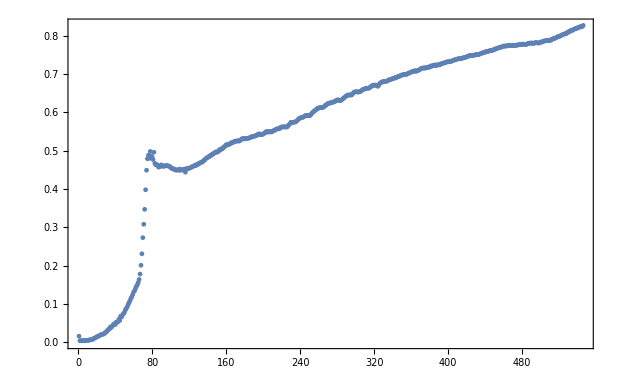

```mathematica
Show[ListPlot[data[All,"A5"]//Normal],Plot[nlm[x],{x,0,500}, PlotStyle->Orange],Frame->True]
```

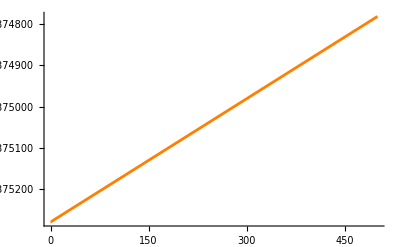

```mathematica
Plot[nlm[x],{x,0,500}, PlotStyle->Orange]
```